```mathematica
(*run first*)
Clear[T,M,r,μ, mD];
eps=1/1000;
R=20000;
Tin=Quiet[Join[Parallelize[Table[{x,-x^2 Quiet[NIntegrate[(2Sin[z x])/(x(z^2+1)),{z,0,∞},WorkingPrecision->32]]},{x,eps/100,2,10eps}]],Parallelize[Table[{x,-x^2 Quiet[NIntegrate[(2Sin[z x])/(x(z^2+1)),{z,0,∞},WorkingPrecision->32]]},{x,2+100eps,10,100eps}]],Parallelize[Table[{x,-x^2 Quiet[NIntegrate[(2Sin[z x])/(x(z^2+1)),{z,0,∞},WorkingPrecision->32]]},{x,10+1000eps,100,10000eps}]],Parallelize[Table[{x,-x^2 Quiet[NIntegrate[(2Sin[z x])/(x(z^2+1)),{z,0,∞},WorkingPrecision->32]]},{x,100+100000eps,10000,100000eps}]],Parallelize[Table[{x,-x^2 Quiet[NIntegrate[(2Sin[z x])/(x(z^2+1)),{z,0,∞},WorkingPrecision->32]]},{x,10000+10000000eps,1000000,10000000eps}]]]];
TIm1=Quiet[ Join[Parallelize[Table[{x,Quiet[NIntegrate[z/(z^2+1)^2(1-Sin[x*z]/(x*z)),{z,0,∞},WorkingPrecision->32]]},{x,eps/100,2,10eps}]],Parallelize[Table[{x,Quiet[NIntegrate[z/(z^2+1)^2(1-Sin[x*z]/(x*z)),{z,0,∞},WorkingPrecision->32]]},{x,2+100eps,10,100eps}]],Parallelize[Table[{x,Quiet[NIntegrate[z/(z^2+1)^2(1-Sin[x*z]/(x*z)),{z,0,∞},WorkingPrecision->32]]},{x,10+1000eps,100,10000eps}]],Parallelize[Table[{x,Quiet[NIntegrate[z/(z^2+1)^2(1-Sin[x*z]/(x*z)),{z,0,∞},WorkingPrecision->32]]},{x,100+100000eps,10000,100000eps}]],Parallelize[Table[{x,Quiet[NIntegrate[z/(z^2+1)^2(1-Sin[x*z]/(x*z)),{z,0,∞},WorkingPrecision->32]]},{x,10000+10000000eps,1000000,10000000eps}]]]];
```

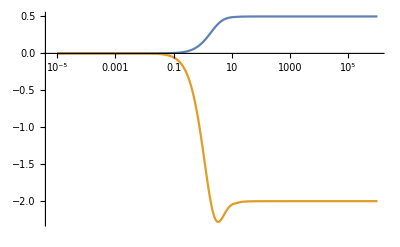

```mathematica
Print[ListLogLinearPlot[{TIm1,Tin},Joined->True, PlotRange->All]];
```

```mathematica
Clear[ParabolicCylinderI,ParabolicCylinderR];
ParabolicCylinderI[r_]=If[r<20,ParabolicCylinderD[-1/2,ⅈ √2 r],ⅇ^(r^2/2) (((1-ⅈ) √(1/r))/2^(3/4)+((3/16-(3 ⅈ)/16) (1/r)^(5/2))/2^(3/4)+((105/512-(105 ⅈ)/512) (1/r)^(9/2))/2^(3/4)+((3465/8192-(3465 ⅈ)/8192) (1/r)^(13/2))/2^(3/4)+((675675/524288-(675675 ⅈ)/524288) (1/r)^(17/2))/2^(3/4))];
ParabolicCylinderR[r_]=ParabolicCylinderD[-1/2,√2 r];
```

```mathematica
TableT[sigma1_,alpha1_, mD1_]:=Module[{sigma=sigma1, alpha=alpha1,mD=mD1},eps=0.001;
μ=(sigma/alpha mD^2)^(1/4);
ratio=mD/μ;R=20000;
(* build tables for the functions  *)
f=Interpolation[Tin,InterpolationOrder->1];
Print[f[10000]];
pg=1;
c=Re[ParabolicCylinderI[eps] NIntegrate[( +1/ratio^2f[ratio x])ParabolicCylinderR[x],{x,eps,R},PrecisionGoal->pg]];
Print[c];
TIm=Join[Parallelize[Table[{r,Quiet[(c-Re[ParabolicCylinderI[r]] NIntegrate[(1/ratio^2 f[ratio x])ParabolicCylinderR[x],{x,r,R},PrecisionGoal->pg]- ParabolicCylinderR[ r](NIntegrate[( 1/ratio^2 f[ratio x])Re[ParabolicCylinderI[x]],{x,eps,r},PrecisionGoal->pg]))]},{r,eps/100,1,10eps}]],Parallelize[Table[{r,Quiet[(c-Re[ParabolicCylinderI[r]] NIntegrate[(1/ratio^2 f[ratio x])ParabolicCylinderR[x],{x,r,R},PrecisionGoal->pg]- ParabolicCylinderR[ r](NIntegrate[( 1/ratio^2 f[ratio x])Re[ParabolicCylinderI[x]],{x,eps,r},PrecisionGoal->pg]))]},{r,1+100eps,10+eps,100eps}]],Parallelize[Table[{r,Quiet[(c-Re[ParabolicCylinderI[r]] NIntegrate[(1/ratio^2 f[ratio x])ParabolicCylinderR[x],{x,r,R},PrecisionGoal->pg]- ParabolicCylinderR[ r](NIntegrate[( 1/ratio^2 f[ratio x])Re[ParabolicCylinderI[x]],{x,eps,r},PrecisionGoal->pg]))]},{r,11,100,1}]],Parallelize[Table[{r,Quiet[(c-Re[ParabolicCylinderI[r]] NIntegrate[(1/ratio^2 f[ratio x])ParabolicCylinderR[x],{x,r,R},PrecisionGoal->pg]- ParabolicCylinderR[ r](NIntegrate[( 1/ratio^2 f[ratio x])Re[ParabolicCylinderI[x]],{x,eps,r},PrecisionGoal->pg]))]},{r,200,1000,100}]],Parallelize[Table[{r,Quiet[(c-Re[ParabolicCylinderI[r]] NIntegrate[(1/ratio^2 f[ratio x])ParabolicCylinderR[x],{x,r,R},PrecisionGoal->pg]- ParabolicCylinderR[ r](NIntegrate[( 1/ratio^2 f[ratio x])Re[ParabolicCylinderI[x]],{x,eps,r},PrecisionGoal->pg]))]},{r,2000,20000,1000}]]];Print[ListLogLinearPlot[Abs[TIm],Joined->True, PlotRange->All]]
(*Print[T];*)];
```

```mathematica
al=0.50425;
s=0.172606;
```

-2.0000000400000047111160798146633

-2.32929

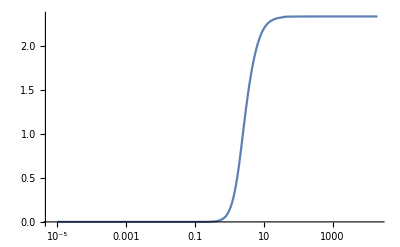

{17.0053,Null}

```mathematica
TableT[0.172606,0.50425,0.09553903263288155]//Timing
```

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

Clear[Nf,m4,M,μ,Mref];
(*QCD*)
Nc=3.;CA=Nc;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68Nc^2+20Nc Nf+12CF Nf)/(3*32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=1/4(3 CF);
γ1[Nf_]=1/16(202/3-20/9Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-8  β0[Nf]/2/ (4π)^2;
b1[Nf_]=-32 β1[Nf]/2 /(4π)^4;

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]);
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5t^3)+1/(β0[Nf]^7t^4)( β1[Nf]^3(-Log[t]^3+5/2Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+β3[Nf] β0[Nf]^2/2);
μ0=2;
t0=Log[μ0^2]; tf=10000*t0;
μref=2;
tref=Log[μref^2/ΛQCD^2];
mref=Log[Mref];
(*solution of the RG equation to 3 loop*)
Print["g"]
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=NDSolve[{ D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000];

Print["ln(m)"];
a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1]; 

mD[μ_,T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[μ T]T+1/(4 π)Nc g4[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[μ T]]+c g4[μ T]^2 T+   d g4[μ T]^3 T ];(* g_s *)
```

g

NDSolve::precw: The precision of the differential equation ({{as'[t]==1/12 as[t]^2 (-33.+2 If[«3»])+1/96 as[t]^3 (-612.+76. If[«3»])+1/128 as[t]^4 (-2857+5033/9 If[«3»]-325/27 Power[«2»])+1/256 as[t]^5 (-149753/6-1093/729 Power[«2»]-3564 Zeta[«1»]-Power[«2»] Plus[«2»]+If[«3»] Plus[«2»]),as[10000 Log[4]]==0.0000376185},{},{},{},{}}) is less than WorkingPrecision (32.).

NDSolve::ndsz: At t == 2.05914, step size is effectively zero; singularity or stiff system suspected.

ln(m)

```mathematica
mD
rev0[1000]+2M
Re[V[20]]+2 M
```

mD

2 M+rev0[1000]

2 M+Re[V[20]]

```mathematica
Tmu[2]
```

Tmu[2]

```mathematica
nF=3;
```

```mathematica
mD[2 π, 0.147, 0.8393566559653528,-0.40422148023272036]
```

0.095539

```mathematica
(* loop over T *)
```

```mathematica
(*parameters*)
Clear[c];
(*{Mb=4.882,Mc=1.47164;A->0.50425,S->0.172606,Cv->-0.176696}*)
M=1.47164;
al=0.50425;
s=0.172606;
constshift=-0.176696;
iT=0;
```

```mathematica
mu=mD[2 π, 0.147, 0.8393566559653528,-0.40422148023272036]
```

0.095539

-2.0000000400000047111160798146633

-2.32929

-Graphics-

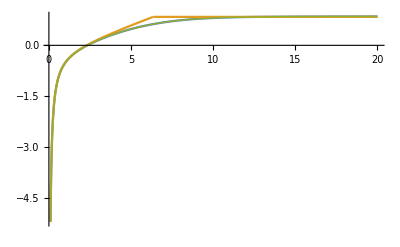

Plot::exclul: {0.095539 r z-0} must be a list of equalities or real-valued functions.

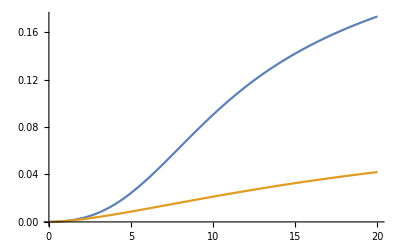

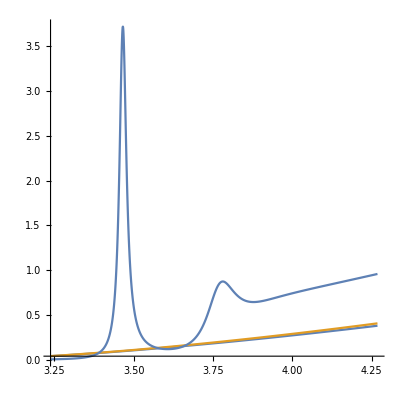

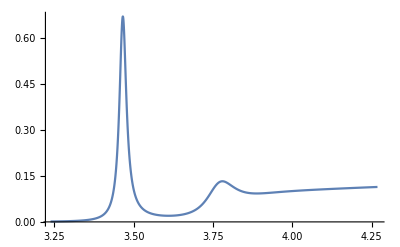

```mathematica
T=0.147;
iT=1;
TT[iT]=T;
(*T=TmD[[chooseT]][[1]];
mu=TmD[[chooseT]][[2]];
T=mDatTc[[1]];
mu=mDatTc[[2]];*)
nF=3;

mu=mD[2 π, T, 0.8393566559653528,-0.40422148023272036];
Tmu[iT]=mu;
Nc=3;
Lmsb=0.3;
(*g=√((8 π^2)/(9 Log[9.082 T/Lmsb]));
mD=√((4 π^2 T^2)/(3 Log[7.547 T/Lmsb]));*)
C1=Gamma[0.25]/(Gamma[0.75]*2);
C2=Gamma[0.25]/(√π*2^(3/4));
(* r, mu in GeV, s in GeV^2*)
k=0;

(*mD[μ_,T_,cc_,dd_]=Sqrt[Nc/3+nF/6]g[μ T]T+1/(4 π)Nc g[μ T]^2 T Log[Sqrt[Nc/3+nF/6]/g[μ T]]+cc g[μ T]^2 T+   dd g[μ T]^3 T;
mu=mD[5.842450954533253,T,0.4254807453130375,-0.13492441570999153]*)
(*table for mD*)

rstringbreak=1.25/0.197; (*fm->GeV*)
rev0[r_]:=If[r<rstringbreak,-(al/(r))+s*r+constshift,-(al/(rstringbreak))+s*rstringbreak+constshift];
TableT[s,al, mu];

REV[r_]:=(s/(mu^2 s/al)^(1/4))*(C1-C2*ParabolicCylinderD[-1/2,(4mu^2 s/al)^(1/4)*(r)])-(al/(r))*(Exp[-(mu*(r))]+(mu*(r)))+constshift;
rev=Interpolation[Join[Table[{r,(s/(mu^2 s/al)^(1/4))*( C1-C2*ParabolicCylinderD[-1/2,(4mu^2 s/al)^(1/4)*(r)])-(al/(r ))*(Exp[-(mu*(r ))]+(mu*(r )))+constshift},{r,0.001,10,0.01}],Table[{r,(s/(mu^2 s/al)^(1/4))*( C1-C2*ParabolicCylinderD[-1/2,(4mu^2 s/al)^(1/4)*(r)])-(al/(r ))*(Exp[-(mu*(r ))]+(mu*(r )))+constshift},{r,10.1,25,0.1}],Table[{r,(s/(mu^2 s/al)^(1/4))*( C1-C2*ParabolicCylinderD[-1/2,(4mu^2 s/al)^(1/4)*(r)])-(al/(r ))*(Exp[-(mu*(r ))]+(mu*(r)))+constshift},{r,26,1000,1}],Table[{r,(s/(mu^2 s/al)^(1/4))*( C1-C2*ParabolicCylinderD[-1/2,(4mu^2 s/al)^(1/4)*(r)])-(al/(r ))*(Exp[-(mu*(r ))]+(mu*(r)))+constshift},{r,1010,20000,10}]],InterpolationOrder->1];
Impot=Interpolation[TIm,InterpolationOrder->1];
Impot1=Interpolation[TIm1,InterpolationOrder->1];
V[x_]:=rev[x]+I T*2*(al) Impot1[mu x]-  I al T*Impot[(mu^2 s/al)^(1/4) x];
fitfIm[x_]:=T*al*2*NIntegrate[z/(z^2+1)^2(1-Sin[x*mu* z]/(x*mu* z)),{z,0,∞}];
Print[Plot[{REV[r],rev0[r],Re[V[r]]},{r,0.1,20},PlotStyle->{Automatic,Automatic,Thick},PlotRange->All]];
Econt[iT]=Re[V[1000]]+2M;
Print[Plot[{Im[V[r]],fitfIm[r]},{r,0.1,20},PlotRange->All]];
Econt[iT]=Re[V[1000]]+2M;
Clear[w,p0,p1,res2];
eps=10^-2; 
l=1; it=0; dw=0.0002;wmin= 0.2M;wmax=0.9 M;
res2=Table[{0,0},{w, wmin, wmax,dw M}];
SetSharedVariable[res2];


ParallelDo[w=wmin+(it-1) dw M;inf=40+500*it*dw;
s0=NDSolve[{(w-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[eps]==2 eps(al M)^2-3 eps^2  (M al)^3/4,
 gr[eps]== eps^2(al M)^2-eps^3  (M al)^3/4},gr,{r,eps,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;
(*Plot[{Re[gr1[r]],Im[gr1[r]]},{r,eps,inf},PlotRange->All];*)
s1=NDSolve[{rho'[r]==(18 Nc M al^4)/(4 π)Im[1/(gr1[r])^2],rho[eps]==0},rho,{r,eps,inf},PrecisionGoal->10,MaxSteps->1000000];

rho2[r_]=(rho[r]/.s1)_⟦1⟧;
(*Print[Plot[rho2[r],{r,eps,inf}]];*)
res2[[it]]={w+2M,rho2[inf]},{it,1,Length[res2]}];


Clear[w,nF];
β=1/T; μ=0;
nF[x_]=1/(ⅇ^(β x)+1);
rhot[w_]=-Nc/(8π)(((w^2+4M w)^(3/2))/(2M+w)) (ⅇ^(β (2 M+w))-1)nF[w/2+M+μ]*nF[w/2+M-μ] UnitStep[w];
rholim[w_]=-Nc/(2π)((w)^(3/2)M^(1/2))  UnitStep[w]; (*NRQCD free spectra *)
p1=ListPlot[Table[{res2[[i]][[1]],res2[[i]][[2]]},{i,1,Length[res2]}],Joined->True, PlotRange->All];
p0=ParametricPlot[{{w+2 M,-rhot[w]/M^2},{w+2 M,-rholim[w]/M^2}},{w,wmin, wmax},PlotRange->All];
Print[Show[p0,p1,AspectRatio->1]];
Print[Show[ListPlot[Table[{res2[[i]][[1]],M^2 res2[[i]][[2]]/(res2[[i]][[1]])^2},{i,1,Length[res2]}],Joined->True,PlotRange->All]]];
TrhodyT[iT]=Table[{res2[[i]][[1]],M^2 res2[[i]][[2]]/(res2[[i]][[1]])^2},{i,1,Length[res2]}];
```

```mathematica
Tscan=Table[TrhodyT[it],{it,1,iT}];
Export["/users/davidlafferty/Desktop/check.dat",Tscan];
```

```mathematica
Tscan={0};
Tscan[[1]]=ToExpression[Import["/users/davidlafferty/Desktop/check.dat","TSV"][[1]]];
```

```mathematica
(*Tscan[[1]]=Tscan[[1]]/.{a_,b_}:>{a,b a^2};*)
```

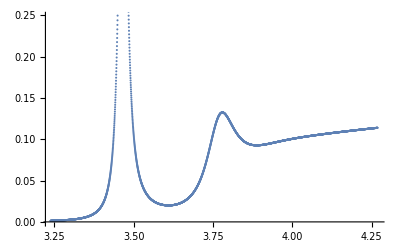

```mathematica
ListPlot[Tscan[[1]]]
```

```mathematica
(*reinit parameters*)
C1=Gamma[0.25]/(Gamma[0.75]*2);
C2=Gamma[0.25]/(√π*2^(3/4));
Clear[c];
(*{Mb=4.882,Mc=1.47164;A->0.50425,S->0.172606,Cv->-0.176696}*)
nF=3;
M=1.47164;
al=0.50425;
s=0.172606;
constshift=-0.176696;
iT=1;
T=0.147;
TT[iT]=T;rev=Interpolation[Join[Table[{r,(s/(mu^2 s/al)^(1/4))*( C1-C2*ParabolicCylinderD[-1/2,(4mu^2 s/al)^(1/4)*(r)])-(al/(r ))*(Exp[-(mu*(r ))]+(mu*(r )))+constshift},{r,0.001,10,0.01}],Table[{r,(s/(mu^2 s/al)^(1/4))*( C1-C2*ParabolicCylinderD[-1/2,(4mu^2 s/al)^(1/4)*(r)])-(al/(r ))*(Exp[-(mu*(r ))]+(mu*(r )))+constshift},{r,10.1,25,0.1}],Table[{r,(s/(mu^2 s/al)^(1/4))*( C1-C2*ParabolicCylinderD[-1/2,(4mu^2 s/al)^(1/4)*(r)])-(al/(r ))*(Exp[-(mu*(r ))]+(mu*(r)))+constshift},{r,26,1000,1}],Table[{r,(s/(mu^2 s/al)^(1/4))*( C1-C2*ParabolicCylinderD[-1/2,(4mu^2 s/al)^(1/4)*(r)])-(al/(r ))*(Exp[-(mu*(r ))]+(mu*(r)))+constshift},{r,1010,20000,10}]],InterpolationOrder->1];
Econt[iT]=Re[rev[1000]]+2M;


mu=mD[2 π, T, 0.8393566559653528,-0.40422148023272036];
Tmu[iT]=mu;
(*T=T+0.002*)
(*Tscan1=Import["/users/lppc/yburnier/travail/a44_Pwave/res_charm/Tscan.dat","Table"];*)
nT=1;
(*Tscan=Table[Table[{ToExpression[StringJoin[Tscan1[[nT]][[it]], Tscan1[[nT]][[it+1]]]][[1]],ToExpression[StringJoin[Tscan1[[nT]][[it]], Tscan1[[nT]][[it+1]]]][[2]]},{it,1,Length[Tscan1[[nT]]],2}],{nT,1,Length[Tscan1]}]*)
```

```mathematica
BW[w_,wr_,Γ_,deltabg_,const_,shift_,shift2_]=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)+2  deltabg((Γ/2)(w-wr))/((w-wr)^2+(Γ/2)^2)+0 ((4 (w-wr)^2- Γ^2) deltabg^2)/(4 (w-wr)^2+Γ^2))+Abs[shift]   (w-wr)+shift2 ;
BWi[w_,wr_,Γ_,const_]=const((Γ/2)^2/((w-wr)^2+(Γ/2)^2)) ;
(*BW[w_,wr_,Γ_,deltabg_,const_]=const Sin[Re[ArcSin[√((Γ/2)^2/((w-wr)^2+(Γ/2)^2))]]+deltabg]^2;*)
```

```mathematica
1/0.15
```

6.66667

```mathematica
0.015 0.15^2
```

0.0003375

```mathematica
shiftfit[1]
```

shiftfit[1]

{0.565537,0.21252,0.150725,0.0848853}

1

2

crit width: bound if>0 {0.359915,-0.0757301}here T= 0.147

Real pot crit: bound if>0 {0.333367,0.0306533}here T= 0.147

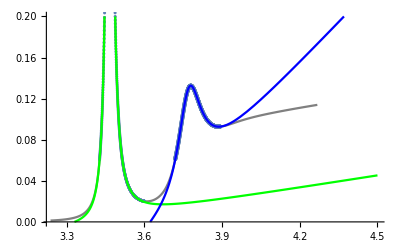

crit area: bound if>0.5 {-0.0490984,0.0726143}

{-1.60848×10^-12,1.14019×10^-13}

-0.0708863

```mathematica
(* charm at Tc middle mD*)
it=1;
Clear[p,nB, prob,w];rhomax=0.2;nF=3;
areaT0={0.565537338089028,0.21252001685922028,0.15072471850495728,0.08488531324802936}(*%%%%%%%% to be changed!! *)
k=1;T=TT[it];
cut=0.06*0.15/T;
nB[w_,T_]=1/(Exp[w/T]-1);
data1=Tscan[[it]];
data=Table[{data1[[n]][[1]],data1[[n]][[2]] (*nB[data1[[n]][[1]],T]/nB[2 M,T]*)},{n,1,Length[data1]}];
For[i=0,i<Length[data]-1,i++; If[data[[i]][[2]]<cut,a[k]=i,b[k]=i];If[(data[[i]][[2]]>cut)&&(data[[i+1]][[2]]<cut),k++]

];
data=Tscan[[it]];
intervals=Table[{a[k1],a[k1]+IntegerPart[4000*T]},{k1,1,k}];
(*intervals[[k]][[2]]=intervals[[k]][[1]]+200;*)
For[i=0,i<Length[intervals],i++;Print[i];
FitPeaki[CurSet][i]= NonlinearModelFit[data[[intervals[[i]][[1]];;intervals[[i]][[2]]]],{BWi[w,wr,Γ,const]},{{wr,data[[Floor[(intervals[[i]][[1]]*0.9+0.1*intervals[[i]][[2]])]]][[1]]},{Γ,(-data[[intervals[[i]][[1]]]][[1]]+data[[intervals[[i]][[2]]]][[1]])/10},{const,2}},w ,MaxIterations->20000,Method->LevenbergMarquardt];FitPeak[CurSet][i]= NonlinearModelFit[data[[intervals[[i]][[1]];;intervals[[i]][[2]]]],{BW[w,wr,Γ,deltabg,const,shift,shift2]},{{wr,wr/.FitPeaki[CurSet][i]["BestFitParameters"]},{Γ,Γ/.FitPeaki[CurSet][i]["BestFitParameters"]},{deltabg,0.0},{const,const/.FitPeaki[CurSet][i]["BestFitParameters"]},{shift,0.05},{shift2,0.01}},w ,MaxIterations->20000,Method->LevenbergMarquardt];
constfit[i]=const/.FitPeak[CurSet][i]["BestFitParameters"];
wrfit[i]=wr/.FitPeak[CurSet][i]["BestFitParameters"];
gammafit[i]=Γ/.FitPeak[CurSet][i]["BestFitParameters"];
deltafit[i]=deltabg/.FitPeak[CurSet][i]["BestFitParameters"];
shiftfit[i]=shift/.FitPeak[CurSet][i]["BestFitParameters"];
p[i]=ListPlot[data[[intervals[[i]][[1]];;intervals[[i]][[2]]]],PlotRange->{0,rhomax}];

pp[i]=Plot[BW[w,wr,Γ,deltabg,const,shift,shift2]/.FitPeak[CurSet][i]["BestFitParameters"],{w,3.2,4.5},PlotStyle->Hue[i/3],PlotRange->{0,rhomax}];
area[i]= π constfit[i]gammafit[i]/2;
prob[i]= π constfit[i]gammafit[i]/2 nB[wrfit[i],0.155](*2 π const/Γ/.FitPeak[CurSet][i]["BestFitParameters"]*)];
Bindingc[it]=Table[Econt[it]-wrfit[i],{i,1,Length[intervals]}];
Widthc[it]=Table[gammafit[i],{i,1,Length[intervals]}];
WPeakc[it]=Table[wrfit[i],{i,1,Length[intervals]}];
Areac[it]=Table[area[i],{i,1,Length[intervals]}];
IsBoundc[it]=Table[Econt[it]-wrfit[i]-gammafit[i],{i,1,Length[intervals]}];
Print["crit width: bound if>0 ", IsBoundc[it], "here T= ", T];
Print["Real pot crit: bound if>0 ",Table[Econt[it]-wrfit[i],{i,1,Length[intervals]}], "here T= ", T];
Print[Show[
Join[{ListPlot[data,PlotRange->{0,rhomax},Joined->True, PlotStyle->Gray]},Flatten[Join[{Table[p[i],{i,1,Length[intervals]}],Table[pp[i],{i,1,Length[intervals]}]}]]],PlotRange->{0,rhomax}]];
Print["crit area: bound if>0.5 ",Table[area[i]/areaT0[[i]],{i,1,Length[intervals]}]];
Print[Table[prob[i],{i,1,Length[intervals]}]];
R0=prob[2]/prob[1];
Print[R0];
```

```mathematica
intervals
```

{{644,1232},{1637,2225}}

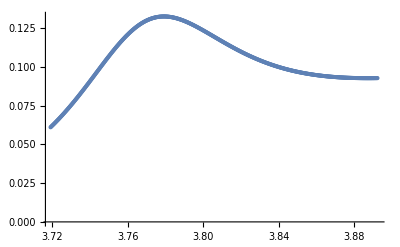

```mathematica
ListPlot[Tscan[[1]][[1637;;2225]]]
```

```mathematica
FitPeak[CurSet][1]["BestFitParameters"]
```

{wr→3.46506,Γ→-0.0265484,deltabg→-0.0331191,const→0.665842,shift→0.0399138,shift2→0.00331308}

```mathematica
FitPeak[CurSet][2]["BestFitParameters"]
```

{wr→3.76777,Γ→0.106383,deltabg→0.137195,const→0.0923481,shift→0.267033,shift2→0.0360751}